GEOMETRICKÁ TRANSFORMÁCIA BODU - ZLOŽITÁ ÚLOHA

==========================================

ZADANIE PRE ŠTUDENTA:

Majme bod P so súradnicami:

{1,4}

Vykonajte postupne tieto transformácie:

1. Vykonajte rotáciu bodu v 2D priestore okolo počiatku súradnicovej sústavy [0,0] o uhol 90°

2. Vykonajte symetriu bodu v 2D priestore podľa priamky 2x + 1y -2 = 0

3. Vykonajte posun bodu v 2D priestore pomocou vektora posunu {7, -5}

RIEŠENIE:

GEOMETRICKÁ TRANSFORMÁCIA BODU - ZLOŽITÁ ÚLOHA

==========================================

POČIATOČNÝ BOD:

Súradnice bodu P:

{1,4}

PRVÁ TRANSFORMÁCIA: Rotácia

GEOMETRICKÉ TRANSFORMÁCIE BODU - ROTÁCIA

========================================

ZADANIE:

Majme bod P so súradnicami:

{1,4}

Vykonajte rotáciu bodu v 2D priestore okolo počiatku súradnicovej sústavy [0,0] o uhol α = 90°.

Transformačná matica rotácie v homogénnych súradniciach:

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1)

TEÓRIA MATICOVÉHO ZOBRAZENIA ROTÁCIE:

Pri rotácii v 2D priestore používame homogénne súradnice, ktoré umožňujú vyjadriť rotáciu ako maticové násobenie:

Transformačná matica rotácie:

(cos(α) | -sin(α) | 0
sin(α) | cos(α) | 0
0 | 0 | 1)

Ak je bod P = [x, y] v základných súradniciach, v homogénnych súradniciach ho zapíšeme ako P = [x, y, 1].
Rotáciu potom môžeme zapísať ako maticové násobenie:

(cos(α) | -sin(α) | 0
sin(α) | cos(α) | 0
0 | 0 | 1) · (x
y
1) = (x·cos(α) - y·sin(α)
x·sin(α) + y·cos(α)
1)

Pre našu hodnotu α = 90°:

cos(α) = 0

sin(α) = 1

VÝPOČET ROTÁCIE BODU:

BOD P:

Pôvodné súradnice: [1, 4]

Homogénne súradnice: [1, 4, 1]

Maticový zápis transformácie bodu P:

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1) |  ·  | (1
4
1) |  =  | (-4
1
1)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 0 | -1 | 0 | ] · [ | 1 | 4 | 1 | ]^T = | -4

= (0 · 1) + (-1 · 4) + (0 · 1)

= (0 · 1) + (-1 · 4) + (0 · 1)

= 0 + -4 + 0

= -4

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 1 | 0 | 0 | ] · [ | 1 | 4 | 1 | ]^T = | 1

= (1 · 1) + (0 · 4) + (0 · 1)

= (1 · 1) + (0 · 4) + (0 · 1)

= 1 + 0 + 0

= 1

• Výpočet homogénnej súradnice (3. riadok matice):

[ | 0 | 0 | 1 | ] · [ | 1 | 4 | 1 | ]^T = | 1

= (0 · 1) + (0 · 4) + (1 · 1)

= (0 · 1) + (0 · 4) + (1 · 1)

= 0 + 0 + 1

= 1

Výsledná homogénna reprezentácia bodu P':

[-4, 1, 1]

Kartézske súradnice bodu P':

[-4, 1]

Alternatívny výpočet pomocou základných vzorcov rotácie:

x' = x·cos(α) - y·sin(α)  =>  1 · 0 - 4 · 1 = -4

y' = x·sin(α) + y·cos(α)  =>  1 · 1 + 4 · 0 = 1

Výsledné súradnice bodu P':

[-4, 1]

--------------------------------------------------

VÝSLEDOK TRANSFORMÁCIE BODU:

Pôvodný bod P:

{1,4}

Rotovaný bod P':

{-4,1}

VIZUALIZÁCIA TRANSFORMÁCIE:

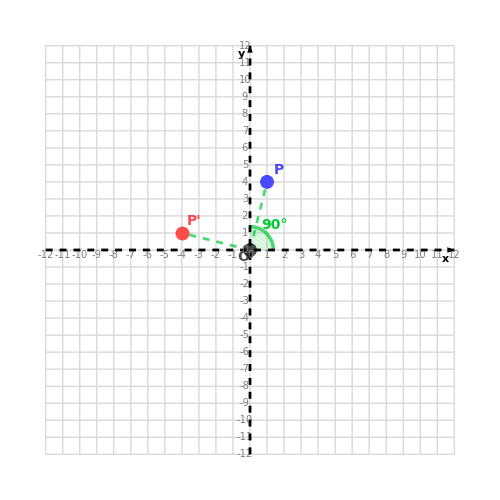

LEGENDA:

• Modré body a čiary: Pôvodný bod

• Červené body a čiary: Rotovaný bod

• Zelené prerušované čiary: Spojnice bodov s počiatkom

• O: Počiatok súradnicovej sústavy - stred rotácie

FAREBNÉ OZNAČENIA V MATICOVÝCH VÝPOČTOCH:

• Červená: Transformačná matica

• Modrá: Vstupné súradnice

• Fialová: Medzivýpočty

• Zelená: Výsledné súradnice

Pôvodný bod (modrá):

Bod P: {1,4}

Výsledný bod (červená):

Bod P': {-4,1}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite rotáciu o opačný uhol:

α' = -α = -90°

MATEMATICKÉ VLASTNOSTI:

• Rotácia okolo počiatku zachováva vzdialenosť všetkých bodov od počiatku sústavy [0,0]

• Rotácia nemení veľkosť ani tvar geometrických útvarov - je to izometria

• Rotácia zachováva uhly medzi úsečkami a ich dĺžky

• Počiatok súradnicovej sústavy [0,0] je fixný bod rotácie - zostáva nezmenený

DRUHÁ TRANSFORMÁCIA: Symetria

GEOMETRICKÉ TRANSFORMÁCIE BODU - SYMETRIA

========================================

ZADANIE:

Majme bod P so súradnicami:

{-4,1}

Vykonajte symetriu v 2D priestore podľa priamky 2x + y - 2 = 0.

TEÓRIA MATICOVÉHO ZOBRAZENIA SYMETRIE:

Pri symetrii podľa priamky ax + by + c = 0 v 2D priestore môžeme použiť homogénnu transformačnú maticu 3×3:

Homogénna transformačná matica pre symetriu má tvar:

((b^2 - a^2)/(a^2 + b^2) | -2ab/(a^2 + b^2) | -2ac/(a^2 + b^2)
-2ab/(a^2 + b^2) | (a^2 - b^2)/(a^2 + b^2) | -2bc/(a^2 + b^2)
0 | 0 | 1)

Výhoda použitia homogénnej matice je, že zahŕňa lineárnu transformáciu aj posun v jednej matici, čo umožňuje

jednoduché reťazenie viacerých transformácií pomocou násobenia matíc.

VÝPOČET TRANSFORMAČNEJ MATICE PRE SYMETRIU:

Pre našu priamku 2x + 1y + -2 = 0:

Vypočítame jednotlivé prvky matice použitím vzorca:

Menovateľ: a^2 + b^2 = 2^2 + 1^2 = 5

Prvý riadok matice:

M[1,1] = (b^2 - a^2)/(a^2 + b^2) = (1 - 4)/(5) = -3/5

M[1,2] = -2ab/(a^2 + b^2) = -2·2·1/(5) = -4/5

M[1,3] = -2ac/(a^2 + b^2) = -2·2·-2/(5) = 8/5

Druhý riadok matice:

M[2,1] = -2ab/(a^2 + b^2) = -2·2·1/(5) = -4/5

M[2,2] = (a^2 - b^2)/(a^2 + b^2) = (4 - 1)/(5) = 3/5

M[2,3] = -2bc/(a^2 + b^2) = -2·1·-2/(5) = 4/5

Tretí riadok matice:

M[3,1] = 0, M[3,2] = 0, M[3,3] = 1 (štandardné hodnoty pre homogénnu transformáciu)

VÝSLEDNÁ TRANSFORMAČNÁ MATICA:

(-3/5 | -4/5 | 8/5
-4/5 | 3/5 | 4/5
0 | 0 | 1)

Pre našu priamku 2x + y - 2 = 0:

a = 2

b = 1

c = -2

VÝPOČET SYMETRIE BODU:

BOD P:

Pôvodné súradnice: [-4, 1]

Výpočet pomocou homogénnej matice:

(-3/5 | -4/5 | 8/5
-4/5 | 3/5 | 4/5
0 | 0 | 1) |  ·  | (-4
1
1) |  =  | (16/5
23/5
1)

Podrobný výpočet súradníc:

• Výpočet novej x-ovej súradnice:

= (-3/5 · -4) + (-4/5 · 1) + (8/5 · 1)

= 12/5 + -4/5 + 8/5

= 16/5

• Výpočet novej y-ovej súradnice:

= (-4/5 · -4) + (3/5 · 1) + (4/5 · 1)

= 16/5 + 3/5 + 4/5

= 23/5

Výsledná reprezentácia bodu P':

[16/5, 23/5]

ŠPECIÁLNE MATICE PRE NIEKTORÉ TYPY SYMETRIÍ:

POSTUP:

Pre výpočet osovej symetrie podľa priamky 2x + y - 2 = 0 používame vzorce:

Všeobecný vzorec pre výpočet symetrie bodu [x, y] podľa priamky ax + by + c = 0:

x' = x - 2a(ax + by + c)/(a^2 + b^2)

y' = y - 2b(ax + by + c)/(a^2 + b^2)

Tento vzorec môžeme zapísať v maticovej forme pomocou homogénnych súradníc [x, y, 1]

ako násobenie s 3×3 maticou, čo umožňuje jednoduché zreťazenie transformácií.

Naše hodnoty koeficientov:

a = 2

b = 1

c = -2

Rovnica osi symetrie: 2x + y - 2 = 0

Normálový vektor osi symetrie: (2, 1)

VÝSLEDOK TRANSFORMÁCIE BODU:

Pôvodný bod P:

{-4,1}

Bod po symetrii P':

{16/5,23/5}

VIZUALIZÁCIA TRANSFORMÁCIE:

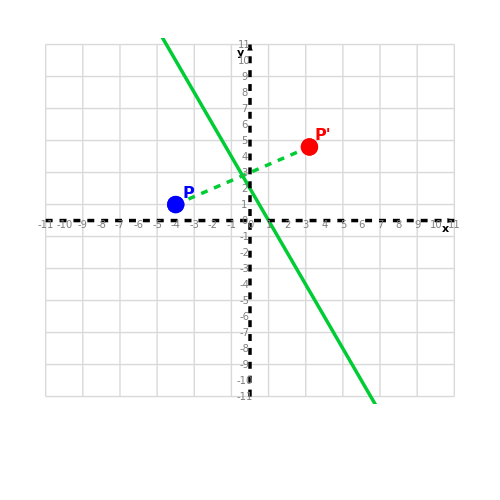

LEGENDA:

• Modré body a čiary: Pôvodný bod

• Červené body a čiary: Bod po symetrii

• Zelené čiara: Os symetrie

• Zelené prerušované čiary: Spojenia zodpovedajúcich si bodov

• Červená: Transformačná matica

• Modrá: Vstupné súradnice

• Fialová: Medzivýpočty

• Zelená: Výsledné súradnice

Pôvodný bod (modrá):

Bod P: {-4,1}

Výsledný bod (červená):

Bod P': {16/5,23/5}

MATEMATICKÉ VLASTNOSTI:

• Symetria podľa priamky je izometrická transformácia - zachováva vzdialenosti medzi bodmi

• Symetria zachováva veľkosť a tvar geometrických útvarov

• Symetria zachováva uhly medzi úsečkami a ich dĺžky

• Body ležiace na osi symetrie zostávajú po symetrii nezmenené

• Aplikovaním symetrie dvakrát získame pôvodný obraz - je to transformácia rádu 2

• Spojnica bodu a jeho obrazu je vždy kolmá na os symetrie

• Stred spojnice bodu a jeho obrazu vždy leží na osi symetrie

VÝZNAMNÉ OSI SYMETRIE:

• Os x (y = 0): bod [x, y] sa zobrazí na [x, -y]

• Os y (x = 0): bod [x, y] sa zobrazí na [-x, y]

• Priamka y = x: bod [x, y] sa zobrazí na [y, x]

• Priamka y = -x: bod [x, y] sa zobrazí na [-y, -x]

TRETIA TRANSFORMÁCIA: Posun

GEOMETRICKÉ TRANSFORMÁCIE BODU - POSUN

========================================

ZADANIE:

Majme bod P so súradnicami:

{16/5,23/5}

Vykonajte posun bodu v 2D priestore pomocou vektora posunu: Δ = [7, -5]

Transformačná matica posunu v homogénnych súradniciach:

(1 | 0 | 7
0 | 1 | -5
0 | 0 | 1)

TEÓRIA MATICOVÉHO ZOBRAZENIA POSUNU:

Pri posune v 2D priestore používame homogénne súradnice, ktoré umožňujú vyjadriť posun ako maticové násobenie:

Transformačná matica posunu:

(1 | 0 | dx
0 | 1 | dy
0 | 0 | 1)

Ak je bod P = [x, y] v základných súradniciach, v homogénnych súradniciach ho zapíšeme ako P = [x, y, 1].
Posun potom môžeme zapísať ako maticové násobenie:

(1 | 0 | dx
0 | 1 | dy
0 | 0 | 1) · (x
y
1) = (x + dx
y + dy
1)

Pre naše hodnoty posunu:

dx = 7 (posun v smere osi x)

dy = -5 (posun v smere osi y)

VÝPOČET POSUNU BODU:

BOD P:

Pôvodné súradnice: [16/5, 23/5]

Homogénne súradnice: [16/5, 23/5, 1]

Maticový zápis transformácie bodu P:

(1 | 0 | 7
0 | 1 | -5
0 | 0 | 1) |  ·  | (16/5
23/5
1) |  =  | (51/5
-2/5
1)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 1 | 0 | 7 | ] · [ | 16/5 | 23/5 | 1 | ]^T = | 51/5

= (1 · 16/5) + (0 · 23/5) + (7 · 1)

= (1 · 16/5) + (0 · 23/5) + (7)

= 16/5 + 0 + 7

= 51/5

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 1 | -5 | ] · [ | 16/5 | 23/5 | 1 | ]^T = | -2/5

= (0 · 16/5) + (1 · 23/5) + (-5 · 1)

= (0 · 16/5) + (1 · 23/5) + (-5)

= 0 + 23/5 + -5

= -2/5

• Výpočet homogénnej súradnice (3. riadok matice):

[ | 0 | 0 | 1 | ] · [ | 16/5 | 23/5 | 1 | ]^T = | 1

= (0 · 16/5) + (0 · 23/5) + (1 · 1)

= (0 · 16/5) + (0 · 23/5) + (1)

= 0 + 0 + 1

= 1

Výsledná homogénna reprezentácia bodu P':

[51/5, -2/5, 1]

Kartézske súradnice bodu P':

[51/5, -2/5]

Alternatívny výpočet pomocou základných vzorcov posunu:

x' = x + dx  =>  16/5 + 7 = 51/5

y' = y + dy  =>  23/5 + -5 = -2/5

Výsledné súradnice bodu P':

[51/5, -2/5]

--------------------------------------------------

VÝSLEDOK TRANSFORMÁCIE BODU:

Pôvodný bod P:

{16/5,23/5}

Posunutý bod P':

{51/5,-2/5}

VIZUALIZÁCIA TRANSFORMÁCIE:

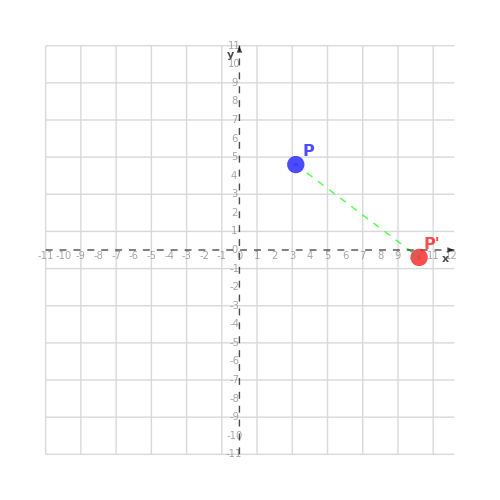

LEGENDA:

• Modré body a čiary: Pôvodný bod

• Červené body a čiary: Posunutý bod

• Zelené prerušované čiary: Posun bodu

FAREBNÉ OZNAČENIA V MATICOVÝCH VÝPOČTOCH:

• Červená: Transformačná matica

• Modrá: Vstupné súradnice

• Fialová: Medzivýpočty

• Zelená: Výsledné súradnice

Pôvodný bod (modrá):

Bod P: {16/5,23/5}

Výsledný bod (červená):

Bod P': {51/5,-2/5}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite vektor posunu:

Δ' = [-7, 5] (opačný vektor)

MATEMATICKÉ VLASTNOSTI:

• Posun zachováva tvar a veľkosť geometrických útvarov

• Posun zachováva vzdialenosti medzi bodmi - je to izometria

• Posun zachováva rovnobežnosť priamok

• Posun zachováva uhly medzi priamkami

• Na rozdiel od rotácie, posun nemá žiadny fixný bod (bod, ktorý zostáva na rovnakom mieste)

POSTUPNÝ VÝPOČET:

Pôvodný bod P:

Súradnice:

{1,4}

Po prvej transformácii (Rotácia):

Súradnice bodu P':

{-4,1}

Po druhej transformácii (Symetria):

Súradnice bodu P'':

{16/5,23/5}

Po tretej transformácii (Posun):

Súradnice bodu P''':

{51/5,-2/5}

VÝPOČET SÚHRNNEJ TRANSFORMAČNEJ MATICE:

Transformačné matice pre jednotlivé transformácie:

Matica pre Rotácia (M1):

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1)

Matica pre Symetria (M2):

(-3/5 | -4/5 | 8/5
-4/5 | 3/5 | 4/5
0 | 0 | 1)

Matica pre Posun (M3):

(1 | 0 | 7
0 | 1 | -5
0 | 0 | 1)

Postupný výpočet súhrnnej matice:

Krok 1: Začíname s maticou prvej transformácie:

M₁ = Matica pre Rotácia

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1)

Krok 2: Násobenie matíc

Pri kompozícii transformácií násobíme matice v opačnom poradí, ako sa aplikujú.

Matica pre aktuálnu transformáciu sa násobí s výsledkom predchádzajúcich transformácií.

M2 · M₁ = Matica pre Symetria · Matica pre Rotácia

Matica pre Symetria (M2):

(-3/5 | -4/5 | 8/5
-4/5 | 3/5 | 4/5
0 | 0 | 1)

Matica prvej transformácie (M₁):

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1)

Výpočet násobenia matíc:

C[1,1] = {(-3/5 × 0) + ,(-4/5 × 1) + ,(8/5 × 0)} = -4/5

C[1,2] = {(-3/5 × -1) + ,(-4/5 × 0) + ,(8/5 × 0)} = 3/5

C[1,3] = {(-3/5 × 0) + ,(-4/5 × 0) + ,(8/5 × 1)} = 8/5

C[2,1] = {(-4/5 × 0) + ,(3/5 × 1) + ,(4/5 × 0)} = 3/5

C[2,2] = {(-4/5 × -1) + ,(3/5 × 0) + ,(4/5 × 0)} = 4/5

C[2,3] = {(-4/5 × 0) + ,(3/5 × 0) + ,(4/5 × 1)} = 4/5

C[3,1] = {(0 × 0) + ,(0 × 1) + ,(1 × 0)} = 0

C[3,2] = {(0 × -1) + ,(0 × 0) + ,(1 × 0)} = 0

C[3,3] = {(0 × 0) + ,(0 × 0) + ,(1 × 1)} = 1

Výsledok násobenia:

(-4/5 | 3/5 | 8/5
3/5 | 4/5 | 4/5
0 | 0 | 1)

Krok 3: Násobenie matíc

M3 · (M2 · ... · M₁) = Matica pre Posun · Výsledok predchádzajúcich transformácií (M2 · ... · M₁)

Matica pre Posun (M3):

(1 | 0 | 7
0 | 1 | -5
0 | 0 | 1)

Výsledok predchádzajúcich transformácií (M2 · ... · M₁):

(-4/5 | 3/5 | 8/5
3/5 | 4/5 | 4/5
0 | 0 | 1)

Výpočet násobenia matíc:

C[1,1] = {(1 × -4/5) + ,(0 × 3/5) + ,(7 × 0)} = -4/5

C[1,2] = {(1 × 3/5) + ,(0 × 4/5) + ,(7 × 0)} = 3/5

C[1,3] = {(1 × 8/5) + ,(0 × 4/5) + ,(7 × 1)} = 43/5

C[2,1] = {(0 × -4/5) + ,(1 × 3/5) + ,(-5 × 0)} = 3/5

C[2,2] = {(0 × 3/5) + ,(1 × 4/5) + ,(-5 × 0)} = 4/5

C[2,3] = {(0 × 8/5) + ,(1 × 4/5) + ,(-5 × 1)} = -21/5

C[3,1] = {(0 × -4/5) + ,(0 × 3/5) + ,(1 × 0)} = 0

C[3,2] = {(0 × 3/5) + ,(0 × 4/5) + ,(1 × 0)} = 0

C[3,3] = {(0 × 8/5) + ,(0 × 4/5) + ,(1 × 1)} = 1

Výsledok násobenia:

(-4/5 | 3/5 | 43/5
3/5 | 4/5 | -21/5
0 | 0 | 1)

VÝSLEDNÁ SÚHRNNÁ TRANSFORMAČNÁ MATICA:

(-4/5 | 3/5 | 43/5
3/5 | 4/5 | -21/5
0 | 0 | 1)

APLIKÁCIA SÚHRNNEJ MATICE NA PÔVODNÝ BOD:

Súhrnná transformačná matica:

(-4/5 | 3/5 | 43/5
3/5 | 4/5 | -21/5
0 | 0 | 1)

Pôvodný bod P:

Súradnice: {1,4}

Postup pri aplikovaní súhrnnej transformačnej matice na bod:

1. Bod (x, y) sa rozšíri na homogénne súradnice (x, y, 1)

2. Vynásobí sa súhrnnou transformačnou maticou 3×3

3. Z výsledného vektora vezmeme prvé dve súradnice, čím dostaneme transformovaný bod

PODROBNÝ VÝPOČET:

Bod P:

Pôvodné súradnice: {1,4}

V homogénnych súradniciach: {1,4,1}

Maticové násobenie:

M · P =

(-4/5 | 3/5 | 43/5
3/5 | 4/5 | -21/5
0 | 0 | 1) · (1
4
1)

Podrobný výpočet:

Riadok 1:

-4/5 · 1 + 3/5 · 4 + 43/5 · 1 = 51/5

Riadok 2:

3/5 · 1 + 4/5 · 4 + -21/5 · 1 = -2/5

Riadok 3:

0 · 1 + 0 · 4 + 1 · 1 = 1

Výsledok pre bod P:

V homogénnych súradniciach: {51/5,-2/5,1}

Transformované súradnice (P'): {51/5,-2/5}

Očakávaný výsledok (P'): {51/5,-2/5}

✓ Výsledok sa zhoduje s očakávaným bodom.

VÝSLEDNÝ TRANSFORMOVANÝ BOD P':

Súradnice: {51/5,-2/5}

Očakávaný výsledný bod:

Súradnice: {51/5,-2/5}

✓ OVERENIE ÚSPEŠNÉ: Transformácia pomocou súhrnnej matice dáva správny výsledok.

ZÁVER:

Použitím jedinej transformácie definovanej súhrnnou maticou sme dosiahli rovnaký výsledok,

ako postupným aplikovaním viacerých transformácií. Tento princíp je kľúčový

v počítačovej grafike a umožňuje efektívne vykresľovanie zložitých transformácií.

SÚHRNNÁ VIZUALIZÁCIA:

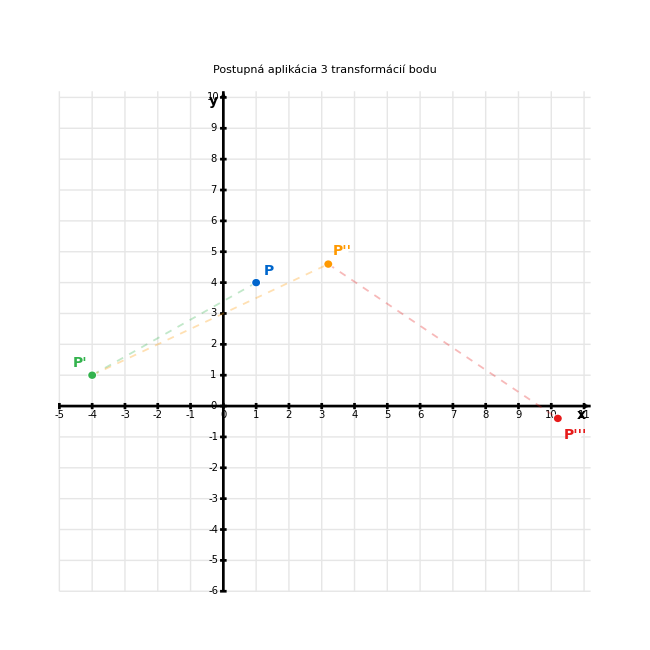

LEGENDA:

• Modré body a čiary: Pôvodný bod P

• Tmavozelené body a čiary: Bod po prvej transformácii (Rotácia)

• Oranžové body a čiary: Bod po druhej transformácii (Symetria)

• Červené body a čiary: Bod po tretej transformácii (Posun)

Postupnosť transformácií:

1. Rotácia o uhol 90°

2. Symetria podľa priamky 2x + 1y -2 = 0

3. Posun o vektor {7, -5}

ZÁVEREČNÝ PREHĽAD:

Vybratá obtiažnosť: Zložitá (3 transformácie)

Vykonali ste tieto transformácie:

1. Rotácia

2. Symetria

3. Posun

Výsledný bod:

{{3,8},-3}

```mathematica
BodTrojitaTransformaciaSVysledkom[]
```